```mathematica
Quiet@Remove["`*"]
```

```mathematica
SetOptions[SelectedNotebook[],PrintingStyleEnvironment->"Printout",ShowSyntaxStyles->True]
```

## Setup

```mathematica
(*Pariapsis: Point of least distance in elliptical orbit
Apoapsis: Point of greatest distance in elliptical orbit*)
```

```mathematica
μE=UnitConvert[Null*PlanetData[Entity["Planet","Earth"], "Mass"],"km^3/s^2"]
```

398600. km^3/s^2

```mathematica
μM=UnitConvert[Null*PlanetaryMoonData[Entity["PlanetaryMoon","Moon"], "Mass"],"km^3/s^2"]
```

4900. km^3/s^2

```mathematica
(*Distance of Satellite's cicular orbit around Earth in Earth system*)
r1=PlanetData[Entity["Planet","Earth"], "Radius"] + 160
```

6531.008 km

```mathematica
(*Distance of Satellite's elliptical orbit around Earth at apoapsis in Earth system*)
r2=PlanetaryMoonData[Entity["PlanetaryMoon","Moon"], "AverageDistanceFromEarth"]
```

385000. km

```mathematica
(*Distance of Satellite's circular orbit around Moon in Moon system*)
```

```mathematica
r3=PlanetaryMoonData[Entity["PlanetaryMoon","Moon"], "Radius"]+100
```

1837.4 km

## Hohmann transfer orbit to the Moon

### Impulse A

```mathematica
(*Speed in circular orbit, distance r1, at point A in Earth system*)
vEarth=√(μE/r1)
```

7.812 km/s

```mathematica
(*Speed in elliptical orbit, distance r1, at point A in Earth system*)
vp=√(μE/r1(2r2)/(r1+r2))
```

11. km/s

```mathematica
(*Necessary Δv in point A, a speed-up of 3.14 km/s*)
ΔvEarth=√(μE/r1)(√((2r2)/(r1+r2))-1)//N(*vp-vEarth*)
```

3.14338 km/s

### Impulse B - neglecting circular motion around moon

```mathematica
(*Speed in elliptical orbit, distance r2, at point B in Earth system*)
va=√(μE/r2(2r1)/(r1+r2))
```

0.186 km/s

```mathematica
(*Speed in circular orbit, distance r2, at point B in Earth system
(i.e. speed of the Moon in Earth system)*)
vNoMoon=√(μE/r2)
```

1.018 km/s

```mathematica
(*Change of speed needed to "follow along with the moon", a speed-up of 0.831 km/s*)
ΔvNoMoon=√(μE/r2)(1-√((2r1)/(r1+r2)))//N(*v3NoMoon-v2B*)
```

0.831657 km/s

### Moon circular orbit correction

```mathematica
(*However we can't follow the moon stationary along it's orbit since the Moon attracts the satellite and it would crash into the surface. We need to go into a circular orbit around the moon*)
```

```mathematica
(*Speed v3 in circular orbit, distance 100 km above the Moon surface, in Moon system*) 
vMoon=√(μM/r3)//N
```

1.63349 km/s

```mathematica
(*We can choose to add or subtract this value to ΔvBNoMoon since we can go around in orbit both ways. Subtracting v3 from ΔvBNoMoon gives numerically the smallest Δv so that's what we'll do*)
```

```mathematica
(*Change in speed needed to go from geocentric elliptical orbit to circular Moon orbit, a speed-down of 0.802 km/s*)
ΔvMoon=ΔvNoMoon-vMoon
```

-0.801832 km/s

### Total

```mathematica
(*Regarding fuel/energy cost, we're interested in in how much we need to change the speed, regardless of direction. Total Δv for the whole trip: impulse at A plus impulse at B*)
ΔvTotal=Abs[ΔvEarth]+Abs[ΔvMoon]//N
```

3.94521 km/s

```mathematica
(*Result if we had neglected the circular motion around the moon at the end. Close, but not identical*)
ΔvTotalNoMoon=Abs[ΔvEarth]+Abs[ΔvNoMoon]
```

3.97504 km/s

### Flight time

```mathematica
tHohmann=UnitConvert[1/2 √((4π^2*((r1+r2)/2)^3)/μE),"Days"]
```

4.99 days

## Trying to minimize ΔvTotal by choosing appropriate moon oribt altitude

```mathematica
RMoon=PlanetaryMoonData[Entity["PlanetaryMoon","Moon"], "Radius"]
```

1737.4 km

### Plot

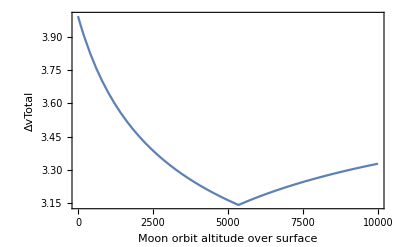

```mathematica
Plot[Abs[√(μE/r1)(√((2r2)/(r1+r2))-1)]+Abs[√(μE/r2)(1-√((2r1)/(r1+r2)))-√(μM/(RMoon+altitude))/.altitude->Quantity[x,"Kilometers"]],{x,0,10^4},Frame->True,FrameLabel->{"Moon orbit altitude over surface","ΔvTotal"}]
```

### Moon orbit altitude that gives minimum ΔvTotal

```mathematica
Solve[√(μE/r2)(1-√((2r1)/(r1+r2)))-√(μM/(RMoon+altitude))==0,altitude]//N
```

{{altitude→5350.99 km}}

### Minimum ΔvTotal

```mathematica
ΔvTotalMin=Abs[√(μE/r1)(√((2r2)/(r1+r2))-1)]+Abs[√(μE/r2)(1-√((2r1)/(r1+r2)))-√(μM/(RMoon+x))/.x->5350.0393315174060602869`2.9098829878759]//N
```

3.14338 km/s

```mathematica
(*Interesting, but a 5350 km altiude Moon orbit is not really relevant for our purposes*)
```

### Moon hill sphere

```mathematica
rHillMoon=N@(PlanetaryMoonData[Entity["PlanetaryMoon","Moon"], "Mass"]/(3*LinguisticAssistant))^(1/3)
```

0.160053

```mathematica
rHillMoon*LinguisticAssistant
```

61618.7 km